```mathematica
σ0=PauliMatrix[0];
σ1=PauliMatrix[1];
σ2=PauliMatrix[2];
σ3=PauliMatrix[3];
```

```mathematica
h0=(-2t Cos[qx]-μ)KroneckerProduct[σ3,σ0]+α Sin[qx]KroneckerProduct[σ0,σ2]-Δ KroneckerProduct[σ2,σ2];
h1=-t KroneckerProduct[σ3,σ0]+ⅈ/2 α KroneckerProduct[σ0,σ1];
HBdGz=Simplify[h0+z h1+z^-1 h1†,{μ∈Reals,t∈Reals,α∈Reals,Δ∈Reals,qx∈Reals}];
HBdGz//MatrixForm
```

(-(t+t z^2+z μ+2 t z Cos[qx])/z | (ⅈ α (-1+z^2-2 z Sin[qx]))/(2 z) | 0 | Δ
(ⅈ α (-1+z^2+2 z Sin[qx]))/(2 z) | -(t+t z^2+z μ+2 t z Cos[qx])/z | -Δ | 0
0 | -Δ | t (1/z+z)+μ+2 t Cos[qx] | (ⅈ α (-1+z^2-2 z Sin[qx]))/(2 z)
Δ | 0 | (ⅈ α (-1+z^2+2 z Sin[qx]))/(2 z) | t (1/z+z)+μ+2 t Cos[qx])

```mathematica
Γ=KroneckerProduct[σ1,ⅈ σ2];
Mx=KroneckerProduct[σ3,-ⅈ σ1];
ΓMx=Γ.Mx;
ΓMx//MatrixForm
```

(0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ
-ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0)

```mathematica
wnum=Table[
param={qx->vqx,μ->vμ,t->1,α->1,Δ->0.5};
sol=Select[Solve[N[Det[HBdGz/.param]]==0,z],Abs[z/.#]<1&];
ΓMxeval=Table[
kernel=NullSpace[(HBdGz/.param)/.sol[[i]],Tolerance->10^-10]//Flatten;
If[Length[kernel]==0,
0,
tmp=Round[(ΓMx.kernel)/kernel];
If[!(Equal@@tmp),Print["error: ",param,", ",i]];
tmp[[1]]
],
{i,4}
];
{vqx,vμ,(Count[ΓMxeval,-1]-Count[ΓMxeval,1])/2},
{vqx,-π,π,π/64},{vμ,-6,6,0.1}
];
wnum=Flatten[wnum,1];
```

Solve::ratnz: Solveは厳密でない係数の系を解くことができませんでした．解は対応する厳密系を解き，結果を数値に変換することで得られました．

General::stop: この計算中に，Solve::ratnzのこれ以上の出力は表示されません．

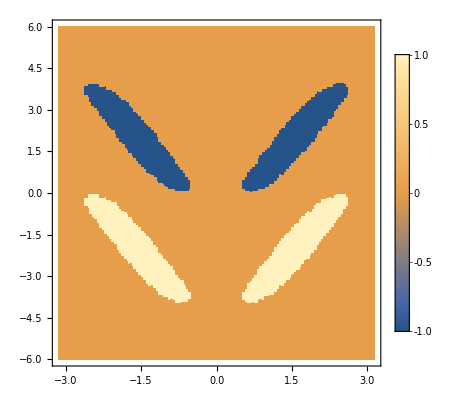

```mathematica
ListDensityPlot[wnum,PlotLegends->Automatic,InterpolationOrder->0]
```